{μ→20,β→0.1,α→0.001,λ→4}

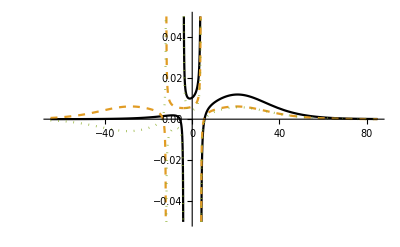

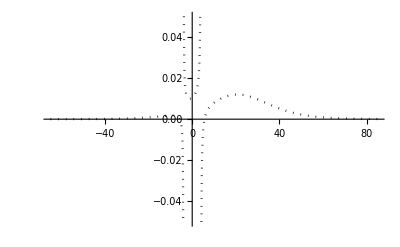

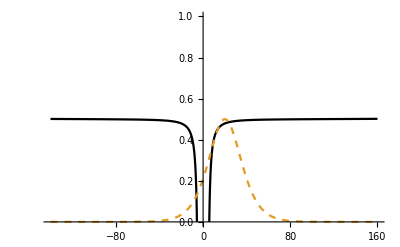

```mathematica
f[ϵ_]:=(β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2));
feven[ϵ_]:=(f[ϵ]+f[-ϵ-2λ])/2
fodd[ϵ_]:=(f[ϵ]-f[-ϵ-2λ])/2

nsubst = {μ->20,β->0.1,α->0.001,λ->4}

Plot[Evaluate[{f[ϵ],feven[ϵ],fodd[ϵ]}/.nsubst],{ϵ,10-75,10+75},PlotStyle->{Black,Dashed,Dotted},PlotRange->{-0.05,0.05}]
Plot[Evaluate[{f[ϵ]}/.nsubst],{ϵ,10-75,10+75},PlotStyle->{Black,Dashed,Dotted},PlotRange->{-0.05,0.05}]

Plot[Evaluate[{(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2)),2 Exp[β(ϵ-μ)]/(1+Exp[β(ϵ-μ)])^2}/.nsubst],{ϵ,10-150,10+150},PlotStyle->{Black,Dashed,Dotted},PlotRange->{0,1}]
```

```mathematica
(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2))//Series[#,{ϵ,∞,2}]&
```

1+(-(2 λ^2)/(π^2 α^2)-λ^2/2)/ϵ^2+O((1/ϵ)^3)

```mathematica
(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2))//Apart
```

(π^2 α^2 ϵ^2)/(2 (π^2 α^2 ϵ^2+4 λ^2))+ϵ/(4 (λ-ϵ))-ϵ/(4 (λ+ϵ))+1

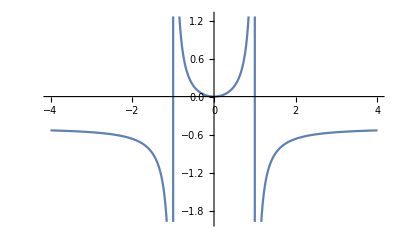

```mathematica
Plot[ϵ/(4 (λ-ϵ))-ϵ/(4 (λ+ϵ))/.λ->1,{ϵ,-4,4}]
```

```mathematica
ϵ/(4 (λ-ϵ))-ϵ/(4 (λ+ϵ))//Together
```

-ϵ^2/(2 (ϵ-λ) (λ+ϵ))

```mathematica
ϵ/(4 (λ-ϵ))-ϵ/(4 (λ+ϵ))+1//Integrate[#,{ϵ,-a,a},PrincipalValue->True,Assumptions->a>λ&&a>0]&//FullForm
```

Plus[a,Times[\[Lambda],ArcTanh[Times[a,Power[\[Lambda],-1]]]]]

```mathematica
Plot[λ tanh^-1(a/λ)+a,{a,0,10}]
```

-Graphics-

```mathematica
(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (λ+ϵ) (π^2 α^2 ϵ^2+4 λ^2))//Apart
```

(π^2 α^2 ϵ^2)/(2 (π^2 α^2 ϵ^2+4 λ^2))+ϵ/(4 (λ-ϵ))-ϵ/(4 (λ+ϵ))+1

```mathematica
x1=(π^2 α^2 ϵ^2)/(2 (π^2 α^2 ϵ^2+4 λ^2))(β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2
x2=(β Exp[β(ϵ-μ)])/(1+Exp[β(ϵ-μ)])^2(ϵ/(4 (λ-ϵ))-ϵ/(4 (λ+ϵ))+1)
```

(π^2 α^2 β ϵ^2 ⅇ^(β (ϵ-μ)))/(2 (π^2 α^2 ϵ^2+4 λ^2) (ⅇ^(β (ϵ-μ))+1)^2)

(β (ϵ/(4 (λ-ϵ))-ϵ/(4 (λ+ϵ))+1) ⅇ^(β (ϵ-μ)))/((ⅇ^(β (ϵ-μ))+1)^2)

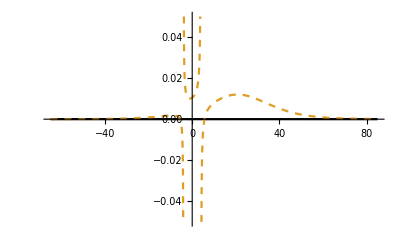

```mathematica
Plot[Evaluate[{x1,x2}/.nsubst],{ϵ,10-75,10+75},PlotStyle->{Black,Dashed,Dotted},PlotRange->{-0.05,0.05}]
```